#### Cost Function for a Linear Propagator Model

0.4

1+6.28319 Cos[π t]

1

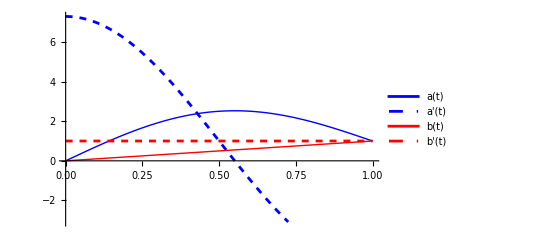

P(t) = 11/10-1.67188 ⅇ^(-10 t)+0.571877 Cos[π t]+0.17966 Sin[π t]

P(0.4) = 1.41697

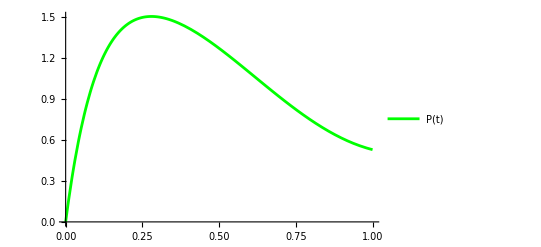

```mathematica
ClearAll["Global`*"]
(*Define the input functions and parameters*)
an ={2.0, 0.0};  
bn = {0, 0};
a[t_]:= t + an[[1]]  Sin[Pi  t] + an[[2]] Sin[2 Pi t];(*Define a(t) here*)
b[t_]:=t +  bn[[1]]  Sin[Pi  t] + bn[[2]] Sin[2 Pi t];(*Define b(t) here*)
lambda= 10(*Define lambda here*);
rho= 10 (*Define rho here*);
t0 = 0.4 (* Define time*)

(*Define derivatives of a(t) and b(t)*)
aPrime[t_]=D[a[t],t]
bPrime[t_]=D[b[t],t]

(*Plot a(t),a'(t),b(t),b'(t) for t in[0,1]*)Plot[{a[t],aPrime[t],b[t],bPrime[t]},{t,0,1},PlotStyle->{{Thick,Blue},{Dashed,Blue},{Thick,Red},{Dashed,Red}},PlotLegends->{"a(t)","a'(t)","b(t)","b'(t)"}]

(*Derive P(t) analytically*)P[t_ ]=Integrate[Exp[-rho (t-s)] (aPrime[s]+lambda bPrime[s]),{s,0,t},Assumptions->{t>=0,rho>0}];

(*Print the analytical formula for P(t)*)
PFormula=P[t]//Simplify;
Print["P(t) = ",PFormula]
Print["P(", t0, ") = ",Chop[P[t0]]]

(* Plot P(t)*)
Plot[P[t], {t, 0,1},
PlotStyle->{Green}, 
PlotLegends->{"P(t)"}]
```

```mathematica
(*Derive the value L(a), L(b)*)
La=Integrate[aPrime[t]*P[t],{t,0,1}];
Lb=Integrate[bPrime[t] lambda *P[t],{t,0,1}];

(*Numeric value of L*)
LaNumeric=N[La];
LbNumeric=N[Lb];

(*Output the results*)
Print["L(a) : ",{La,Chop[LaNumeric]}]
Print["L(b) : ",{Lb,Chop[LbNumeric]}]
Print["P(0.4) : ", Chop[P[0.4]]]
```

L(a) : {1.88765,1.88765}

L(b) : {10.472,10.472}

P(0.4) : 1.41697